{1,4,9,10,16,25,36,40,49,64,81,90}

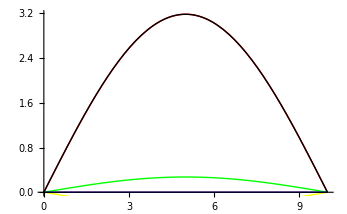

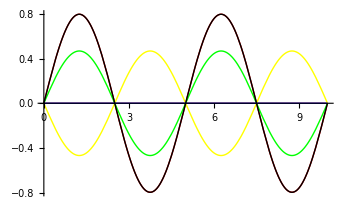

{ee→15.7914+1.39681×10^-8 ⅈ,s1→-6.1371×10^-9+4.44925×10^-9 ⅈ,s2→-0.587168+0.0026157 ⅈ,s3→0.587168-0.0026157 ⅈ,s4→-2.94963×10^-9+3.06447×10^-9 ⅈ,s5→1.+2.81233×10^-11 ⅈ}

```mathematica
Clear[a,k,L, t,t2, data, eigenVals,so,finalVal1,finalVal2,finalVal3,finalVal4,finalVal5,finalVal6]
Clear[f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12]
L=10; (*length*)
endVal = 0;(*the value of the function at the other boundary - you want to adjust energy to match this*)
t = 10;
t2 = 1;
a = 1;
k=0;
so = 1;(*strength of spin orbit coupling*)
Ntmax =3;
listt=Table[t a^2 n^2 ,{n,1,Ntmax}];
listt2=Table[t2 a^2 n^2,{n,1,Floor[√(t/t2)Ntmax]}];
searchEnergyList = Sort[Join[listt,listt2]]

(*EIGENVALS WITH SO = 0: 0.9869604871016626,3.9478419081970575,8.882644113984927,8.882644111651427,15.791367780805407,24.67405646143878,35.53059257435133,35.53134471873784,48.3620862988592,63.16691211136735,79.94347547485177,119.42211735850353*)

(*EIGENVALS WITH SO=1: 0.9869605358025567+8.17973251713015*^-16 ⅈ,3.947841885335814+3.192149647141035*^-11 ⅈ,8.882644296897737-3.169175149882817*^-10 ⅈ,8.882644278023973-2.9373097699642047*^-9 ⅈ,15.791367819102753+2.2980138074686186*^-8 ⅈ,24.67401232052557-5.616634975269799*^-10 ⅈ,35.531376715017835+0.000018151763061893392 ⅈ,35.530578090537006-9.79012604826188*^-9 ⅈ,48.3644378393159+0.0002369786580501262 ⅈ,63.16551875773509+3.9904013835933316*^-7 ⅈ,79.97279347889388-0.024281825449432384 ⅈ,118.81885406428454-0.0076734982874513205 ⅈ*)

(*EIGENVALS WITH SO=10: 0.9869605040831431-5.857200689239565*^-11 ⅈ,3.9478418400917192+8.493641826616396*^-9 ⅈ,8.88264446889651-5.1386228970556435*^-9 ⅈ,8.88264436677564-7.099370663100697*^-8 ⅈ,15.79136752093244+4.122824759279679*^-9 ⅈ,24.67401198855112-6.635557539427162*^-8 ⅈ,35.53192531839091-0.0003675062720358805 ⅈ,35.53053203946908-0.000014518372967001734 ⅈ,48.36102135252454-3.6968352476819233*^-6 ⅈ,63.24329014327483-0.02995732464185087 ⅈ,79.94382600348847-2.7864468508445046*^-6 ⅈ,98.68683455762869+0.006043498347707227 ⅈ*)

(*EIGENVALS WITH SO = 100: 0.9869605640559439+3.832332993734336*^-8 ⅈ,3.9478417587140053+1.3787109489249433*^-9 ⅈ,8.882665359603985-0.00003833694769765802 ⅈ,8.882643390371122+1.4617080509809698*^-7 ⅈ,15.791366385303613+3.1690782532791498*^-9 ⅈ,24.673949790135502-0.00009938858422292066 ⅈ,35.530577143687424-1.697287524477336*^-6 ⅈ,35.40758098531294-0.1370272251428699 ⅈ,48.35924727515167+0.0025793823118783824 ⅈ,63.16571293248686-0.00030307105542130803 ⅈ,79.94435806068257+0.0002089887913210396 ⅈ,94.84785951276498+0.616901517926555 ⅈ*)
data[ee_?NumericQ,slope1_?NumericQ,slope2_?NumericQ,slope3_?NumericQ,slope4_?NumericQ,slope5_?NumericQ]:=NDSolve[
{
f7[x]==f1'[x],
f8[x]==f2'[x],
f9[x]==f3'[x],
f10[x]==f4'[x],
f11[x]==f5'[x],
f12[x]==f6'[x],

f1[0]==0,
f2[0]==0,
f3[0]==0,
f4[0]==0,
f5[0]==0,
f6[0]==0,

f7[0]==1,
f8[0]==slope1,
f9[0]==slope2,
f10[0]==slope3,
f11[0]==slope4,
f12[0]==slope5,

(*({{f1[x]}, {f2[x]}, {f3[x]}, {f4[x]}, {f5[x]}, {f6[x]}})= ({{yz up}, {zx up}, {xy up}, {yz down}, {zx down}, {xy down}})*)
- ee*f1[x]==a^2 k^2 t2 f1[x]+1/3 so (f1[x]+ⅈ f2[x]-f6[x])+a^2  t f7'[x],(*check this extremely carefully*)
- ee*f2[x]==a^2 k^2 t f2[x]+1/3 so (-ⅈ f1[x]+f2[x]+ⅈ f6[x])+a^2 t2 f8'[x],
- ee*f3[x]==a^2 k^2 t f3[x]+1/3 so (f3[x]+f4[x]-ⅈ f5[x])+a^2 t f9'[x],
- ee*f4[x]==a^2 k^2 t2 f4[x]+1/3 so (f3[x]+f4[x]-ⅈ f5[x])+a^2  t f10'[x],
- ee*f5[x]==a^2 k^2 t f5[x]+1/3 so (ⅈ f3[x]+ⅈ f4[x]+f5[x])+a^2 t2 f11'[x],
- ee*f6[x]==a^2 k^2 t f6[x]+1/3 so (-f1[x]-ⅈ f2[x]+f6[x])+a^2 t f12'[x]
},
{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12},
{x,0,L}
]
finalVal1[ee_?NumericQ,s1_?NumericQ,s2_?NumericQ,s3_?NumericQ,s4_?NumericQ,s5_?NumericQ]:=(f1/.First[data[ee,s1,s2,s3,s4,s5]])[L] - endVal;
finalVal2[ee_?NumericQ,s1_?NumericQ,s2_?NumericQ,s3_?NumericQ,s4_?NumericQ,s5_?NumericQ]:=(f2/.First[data[ee,s1,s2,s3,s4,s5]])[L] - endVal;
finalVal3[ee_?NumericQ,s1_?NumericQ,s2_?NumericQ,s3_?NumericQ,s4_?NumericQ,s5_?NumericQ]:=(f3/.First[data[ee,s1,s2,s3,s4,s5]])[L] - endVal;
finalVal4[ee_?NumericQ,s1_?NumericQ,s2_?NumericQ,s3_?NumericQ,s4_?NumericQ,s5_?NumericQ]:=(f4/.First[data[ee,s1,s2,s3,s4,s5]])[L] - endVal;
finalVal5[ee_?NumericQ,s1_?NumericQ,s2_?NumericQ,s3_?NumericQ,s4_?NumericQ,s5_?NumericQ]:=(f5/.First[data[ee,s1,s2,s3,s4,s5]])[L] - endVal;
finalVal6[ee_?NumericQ,s1_?NumericQ,s2_?NumericQ,s3_?NumericQ,s4_?NumericQ,s5_?NumericQ]:=(f6/.First[data[ee,s1,s2,s3,s4,s5]])[L] - endVal;

(*with so=0*)
list = data[0.9869604871016756,1.0228686041457727*^-22,1,1,2.271305483925635*^-22,1];
list2= data[15.791367446441791,-2.9973271122170615*^-10,1.0002021592664068,0.9998853628099266,2.9955502483413795*^-10,1];

(*with so=1*)
list3 = data[0.986960534775759-9.311277413557326*^-21 ⅈ,-2.5399480690265197*^-21+9.252166785009295*^-16 ⅈ,-0.08571456166074204+9.588878959940766*^-9 ⅈ,0.08571456166074204-9.588878959940656*^-9 ⅈ,1.2548197052967667*^-22-4.9874439450334416*^-17 ⅈ,1.-1.4498219844502957*^-21 ⅈ];
list4= data[15.79136760361257+1.396809358389944*^-8 ⅈ,-6.137104788658687*^-9+4.449246537452445*^-9 ⅈ,-0.5871683701521532+0.0026156995650885692 ⅈ,0.5871683701663187-0.0026156995512694272 ⅈ,-2.949630146282967*^-9+3.0644748677028035*^-9 ⅈ,1.000000000020463+2.8123291347774436*^-11 ⅈ];

b1 = Plot[Evaluate[Re[f1[x]]/.list3],{x,0,L},PlotStyle->Red];
b2 = Plot[Evaluate[Re[f2[x]]/.list3],{x,0,L},PlotStyle->Orange];
b3 = Plot[Evaluate[Re[f3[x]]/.list3],{x,0,L},PlotStyle->Yellow];
b4 = Plot[Evaluate[Re[f4[x]]/.list3],{x,0,L},PlotStyle->Green];
b5= Plot[Evaluate[Re[f5[x]]/.list3],{x,0,L},PlotStyle->Blue];
b6= Plot[Evaluate[Re[f6[x]]/.list3],{x,0,L},PlotStyle->Black];
Show[b1,b2,b3,b4,b5,b6](*REMEMBER TO CHANGE THE REFERNCED LIST*)

c1 = Plot[Evaluate[Re[f1[x]]/.list4],{x,0,L},PlotStyle->Red];
c2 = Plot[Evaluate[Re[f2[x]]/.list4],{x,0,L},PlotStyle->Orange];
c3 = Plot[Evaluate[Re[f3[x]]/.list4],{x,0,L},PlotStyle->Yellow];
c4 = Plot[Evaluate[Re[f4[x]]/.list4],{x,0,L},PlotStyle->Green];
c5 = Plot[Evaluate[Re[f5[x]]/.list4],{x,0,L},PlotStyle->Blue];
c6 = Plot[Evaluate[Re[f6[x]]/.list4],{x,0,L},PlotStyle->Black];
Show[c1,c2,c3,c4,c5,c6]

FindRoot[
{
finalVal1[ee,s1,s2,s3,s4,s5]==0,
finalVal2[ee,s1,s2,s3,s4,s5]==0,
finalVal3[ee,s1,s2,s3,s4,s5]==0,
finalVal4[ee,s1,s2,s3,s4,s5]==0,
finalVal5[ee,s1,s2,s3,s4,s5]==0,
finalVal6[ee,s1,s2,s3,s4,s5]==0
},
{
{ee,15.791367446441791},{s1,1},{s2,1},{s3,1},{s4,1},{s5,1}
}
]
,
eigenVals={};
Do[
AppendTo[
eigenVals,
ee/.FindRoot[
{
finalVal1[ee,s1,s2,s3,s4,s5]==0,
finalVal2[ee,s1,s2,s3,s4,s5]==0,
finalVal3[ee,s1,s2,s3,s4,s5]==0,
finalVal4[ee,s1,s2,s3,s4,s5]==0,
finalVal5[ee,s1,s2,s3,s4,s5]==0,
finalVal6[ee,s1,s2,s3,s4,s5]==0
},
{
{ee,searchEnergyList[[i]]},{s1,1},{s2,1},{s3,1},{s4,1},{s5,1}
}
]
],
{i,1,Length[searchEnergyList],1}
]
eigenVals
```

```mathematica
(*vec[x] = ({{f1[x]}, {f2[x]}, {f3[x]}, {f4[x]}, {f5[x]}, {f6[x]}})= ({{yz up}, {zx up}, {xy up}, {yz down}, {zx down}, {xy down}});
deriv[x] = ({{f7[x]}, {f8[x]}, {f9[x]}, {f10[x]}, {f11[x]}, {f12[x]}});
somatrix = ({{1, ⅈ, 0, 0, 0, -1}, {-ⅈ, 1, 0, 0, 0, ⅈ}, {0, 0, 1, 1, -ⅈ, 0}, {0, 0, 1, 1, -ⅈ, 0}, {0, 0, ⅈ, ⅈ, 1, 0}, {-1, -ⅈ, 0, 0, 0, 1}});*)

(*necessary system of equations
({{f7[x]}, {f8[x]}, {f9[x]}, {f10[x]}, {f11[x]}, {f12[x]}})=({{f1'[x]}, {f2'[x]}, {f3'[x]}, {f4'[x]}, {f5'[x]}, {f6'[x]}});
({{f1[x]}, {f2[x]}, {f3[x]}, {f4[x]}, {f5[x]}, {f6[x]}})=({{0}, {0}, {0}, {0}, {0}, {0}});
({{f7[x]}, {f8[x]}, {f9[x]}, {f10[x]}, {f11[x]}, {f12[x]}})=({{1}, {slope1}, {slope2}, {slope3}, {slope4}, {slope5}});

ee ({{f1[x]}, {f2[x]}, {f3[x]}, {f4[x]}, {f5[x]}, {f6[x]}})=  a^2 k^2({{t2*f1[x]}, {t*f2[x]}, {t*f3[x]}, {t2*f4[x]}, {t*f5[x]}, {t*f6[x]}})+a^2({{t*f7'[x]}, {t2*f8'[x]}, {t*f9'[x]}, {t*f10'[x]}, {t2*f11'[x]}, {t*f12'[x]}})+so/3({{1, ⅈ, 0, 0, 0, -1}, {-ⅈ, 1, 0, 0, 0, ⅈ}, {0, 0, 1, 1, -ⅈ, 0}, {0, 0, 1, 1, -ⅈ, 0}, {0, 0, ⅈ, ⅈ, 1, 0}, {-1, -ⅈ, 0, 0, 0, 1}}).({{f1[x]}, {f2[x]}, {f3[x]}, {f4[x]}, {f5[x]}, {f6[x]}});*)
```